## Reading data

```mathematica
nInputData=7370;
```

```mathematica
nOutputData=532;
```

```mathematica
RawGyro=Import["/home/work/local/working/my_stuff/chapchom/private/julio/dead_reckoning/RESLT/raw_gyro.dat"];
```

```mathematica
FilteredGyro=Import["/home/work/local/working/my_stuff/chapchom/private/julio/dead_reckoning/RESLT/filtered_gyro.dat"];
```

```mathematica
RawGyroTable=Table[{RawGyroTime[[i,1]],RawGyroTime[[i,2]] 180.0/π},{i,1,nInputData}];
```

```mathematica
FilteredGyroTable=Table[{FilteredGyro[[i,1]],FilteredGyro[[i,2]] 180.0/π},{i,1,nOutputData}];
```

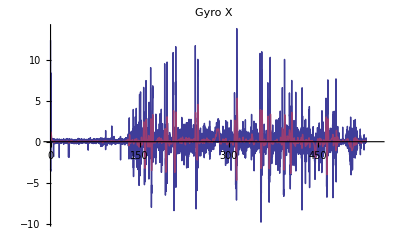

```mathematica
ListLinePlot[{RawGyroTable,FilteredGyroTable},PlotLabel->"Gyro X", PlotRange->{{0,550},All}]
```